```mathematica
SatisfiabilityInstances
```

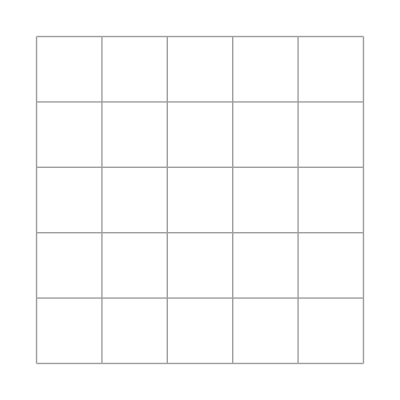

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_back_to_blinker.m"];
looker2=plt[({{xNW11, xN11, xN12, xN13, xNE13}, {xW11, x11, x12, x13, xE13}, {xW21, x21, x22, x23, xE23}, {xW31, x31, x32, x33, xE33}, {xSW31, xS31, xS32, xS33, xSE33}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

```mathematica
Implies
```

```mathematica
⇒
```

```mathematica
cnf[x⇒False]
```

CNF | DNF
¬x | ¬x

```mathematica
life44
```

```mathematica
X0=({{xNW11, xN11, xN12, xN13, xNE13}, {xW11, x11, x12, x13, xE13}, {xW21, x21, x22, x23, xE23}, {xW31, x31, x32, x33, xE33}, {xSW31, xS31, xS32, xS33, xSE33}})/.endGame[[1]];
plt/@NestList[updateLife2[{5,5}][ #]&,
X0,3]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}